### ex 1

#### given

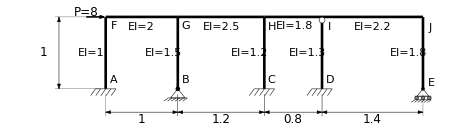

#### soln

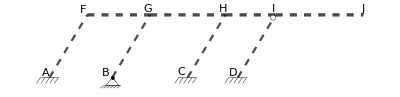
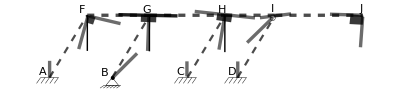
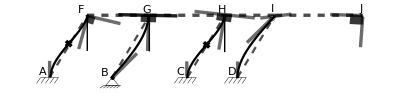
-Graphics-"(a) Sketch the chords (dashed lines)"
-Graphics-"(b) Sketch directions at nodes wherever possible"
-Graphics-"(c) Sketch the columns"

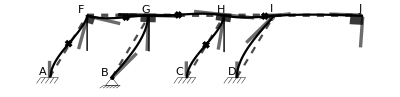
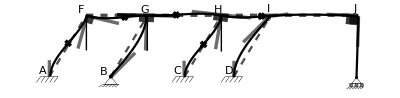
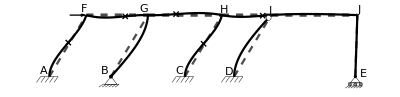
-Graphics-"(d) Sketch the beams"
-Graphics-"(e) Add column with rollers (rigid rotation)"
-Graphics-"(f) Remove extraneous lines (keep chord lines)"

### ex 2

#### given

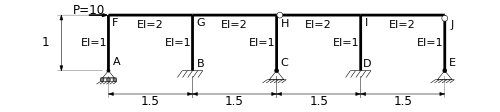

#### soln

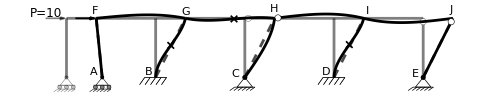

### ex 3 - Spring 2011 exam 2

#### given

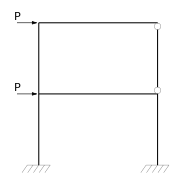
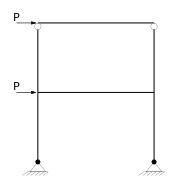

#### solution

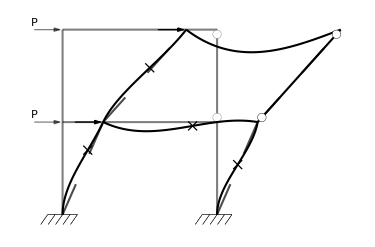

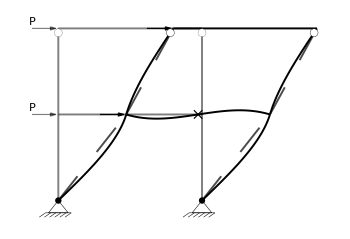

### ex - Fall 2016 class Oct 19, 2016

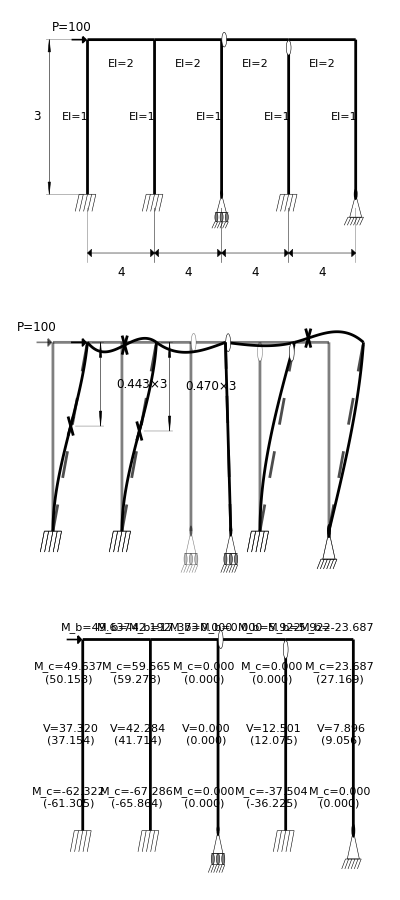

```mathematica
makeBuildingSideLoadedSpecsAndSolutionGrid[ {3}, {4, 4, 4, 4},500,
buildingSupportList -> {1 -> "fixed", 2 -> "fixed",  3  -> "roller", 4 -> "fixed", 5 -> "hinge"},
buildingForceSideMagnitudeList -> {1 -> 100 },
buildingBeamsInternalHingesList -> {{1, 3} -> Left},
buildingColumnsInternalHingesList -> { {1, 4} -> Top  },
buildingBeamsEIMagnitudeList -> {_ -> 2},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingFactorDisplacement -> 2 ]
```

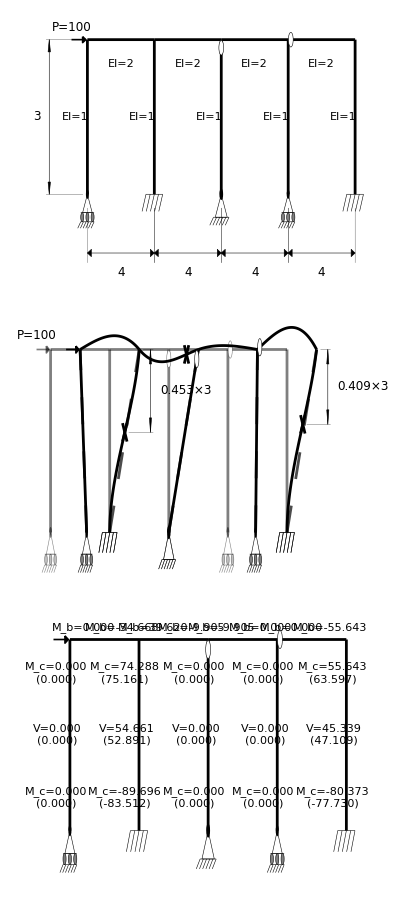

```mathematica
makeBuildingSideLoadedSpecsAndSolutionGrid[ {3}, {4, 4, 4, 4},500,
buildingSupportList -> {1 -> "roller", 2 -> "fixed",  3  -> "hinge", 4 -> "roller", 5 -> "fixed"},
buildingForceSideMagnitudeList -> {1 -> 100 },
buildingBeamsInternalHingesList -> {{1, 4} -> Left},
buildingColumnsInternalHingesList -> { {1, 3} -> Top  },
buildingBeamsEIMagnitudeList -> {_ -> 2},
buildingColumnsEIMagnitudeList -> {_ -> 1},
buildingFactorDisplacement -> 2 ]
```